# Particle in a Finite Box (0-a)

```mathematica
k[e_,u_]:=Sqrt[2*m*(u-e)/hbar^2]
```

```mathematica
κ[e_,u_]:=Sqrt[2*m*e/hbar^2]
```

Testing our definitions

```mathematica
k[e,u]
```

√2 √((m (-e+u))/hbar^2)

```mathematica
κ[e,u]
```

√2 √((e m)/hbar^2)

Define the wavefunctions in each region.

```mathematica
ψI[e_,u_,x_]:=aA*Exp[κ[e,u]*x]
```

```mathematica
ψIII[e_,u_,x_]:=gG*Exp[-κ[e,u]*x]
```

```mathematica
ψII[e_,u_,x_]:=cC*Exp[I*k[e,u]*x]+ dD*Exp[-I*k[e,u]*x]
```

```mathematica
ψI[e,u,x]
```

aA ⅇ^(√2 √((e m)/hbar^2) x)

```mathematica
ψIII[e,u,x]
```

ⅇ^(-√2 √((e m)/hbar^2) x) gG

```mathematica
ψII[e,u,x]
```

dD ⅇ^(-ⅈ √2 √((m (-e+u))/hbar^2) x)+cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x)

```mathematica
D[ψI[e,u,x],x]
```

√2 aA ⅇ^(√2 √((e m)/hbar^2) x) √((e m)/hbar^2)

```mathematica
ψIp[e_,u_,x_]:=√2 aA ⅇ^(√2 √((e m)/hbar^2) x) √((e m)/hbar^2)
```

```mathematica
ψIp[e,u,x]
```

√2 aA ⅇ^(√2 √((e m)/hbar^2) x) √((e m)/hbar^2)

```mathematica
D[ψII[e,u,x],x]
```

-ⅈ √2 dD ⅇ^(-ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)+ⅈ √2 cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)

```mathematica
ψIIp[e_,u_,x_]:=-ⅈ √2 dD ⅇ^(-ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)+ⅈ √2 cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)
```

```mathematica
ψIIp[e,u,x]
```

-ⅈ √2 dD ⅇ^(-ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)+ⅈ √2 cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)

```mathematica
D[ψIII[e,u,x],x]
```

-√2 ⅇ^(-√2 √((e m)/hbar^2) x) gG √((e m)/hbar^2)

```mathematica
ψIIIp[e_,u_,x_]:=-√2 ⅇ^(-√2 √((e m)/hbar^2) x) gG √((e m)/hbar^2)
```

```mathematica
Solve[(ψIp[e,u,0]/ψI[e,u,0])-(ψIIp[e,u,0]/ψII[e,u,0])==0,dD]
```

{{dD→(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))}}

```mathematica
dD=(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))
```

(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))

```mathematica
lhs[e_,u_]:=ψIIIp[e,u,a]/ψIII[e,u,a]
```

```mathematica
lhs[e,u]
```

-√2 √((e m)/hbar^2)

```mathematica
ψIIp[e,u,a]/ψII[e,u,a]
```

(ⅈ √2 cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2)) √((m (-e+u))/hbar^2)-(ⅈ √2 ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)) √((m (-e+u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2)))/(cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2))+(ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2)))

```mathematica
Simplify[(ⅈ √2 cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2)) √((m (-e+u))/hbar^2)-(ⅈ √2 ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)) √((m (-e+u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2)))/(cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2))+(ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2)))]
```

(√2 (e (-1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) m-(-1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) m u+ⅈ (1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) hbar^2 √((e m)/hbar^2) √((m (-e+u))/hbar^2)))/(hbar^2 (-√((e m)/hbar^2)+ⅈ √((m (-e+u))/hbar^2)+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2)) (√((e m)/hbar^2)+ⅈ √((m (-e+u))/hbar^2))))

```mathematica
ExpToTrig[(√2 (e (-1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) m-(-1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) m u+ⅈ (1+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2))) hbar^2 √((e m)/hbar^2) √((m (-e+u))/hbar^2)))/(hbar^2 (-√((e m)/hbar^2)+ⅈ √((m (-e+u))/hbar^2)+ⅇ^(2 ⅈ √2 a √((m (-e+u))/hbar^2)) (√((e m)/hbar^2)+ⅈ √((m (-e+u))/hbar^2))))]
```

(√2 (-e m+m u+ⅈ hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2)+e m Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-m u Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2) Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ e m Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-ⅈ m u Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2) Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]))/(hbar^2 (-√((e m)/hbar^2)+ⅈ √(-(e m)/hbar^2+(m u)/hbar^2)+(√((e m)/hbar^2)+ⅈ √(-(e m)/hbar^2+(m u)/hbar^2)) (Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)])))

```mathematica
Simplify[(√2 (-e m+m u+ⅈ hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2)+e m Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-m u Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2) Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ e m Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-ⅈ m u Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]-hbar^2 √((e m)/hbar^2) √(-(e m)/hbar^2+(m u)/hbar^2) Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]))/(hbar^2 (-√((e m)/hbar^2)+ⅈ √(-(e m)/hbar^2+(m u)/hbar^2)+(√((e m)/hbar^2)+ⅈ √(-(e m)/hbar^2+(m u)/hbar^2)) (Cos[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)]+ⅈ Sin[2 √2 a √(-(e m)/hbar^2+(m u)/hbar^2)])))]
```

(√2 (hbar^2 √((e m)/hbar^2) √((m (-e+u))/hbar^2) Cos[√2 a √((m (-e+u))/hbar^2)]+m (e-u) Sin[√2 a √((m (-e+u))/hbar^2)]))/(hbar^2 (√((m (-e+u))/hbar^2) Cos[√2 a √((m (-e+u))/hbar^2)]+√((e m)/hbar^2) Sin[√2 a √((m (-e+u))/hbar^2)]))

```mathematica
rhs[e_,u_]:=(√2 (hbar^2 √((e m)/hbar^2) √((m (-e+u))/hbar^2) Cos[√2 a √((m (-e+u))/hbar^2)]+m (e-u) Sin[√2 a √((m (-e+u))/hbar^2)]))/(hbar^2 (√((m (-e+u))/hbar^2) Cos[√2 a √((m (-e+u))/hbar^2)]+√((e m)/hbar^2) Sin[√2 a √((m (-e+u))/hbar^2)]))
```

Now put in some nuclear numbers.....

```mathematica
hbar=197.32
```

197.32

```mathematica
m=938.
```

938.

```mathematica
a=1.0
```

1.

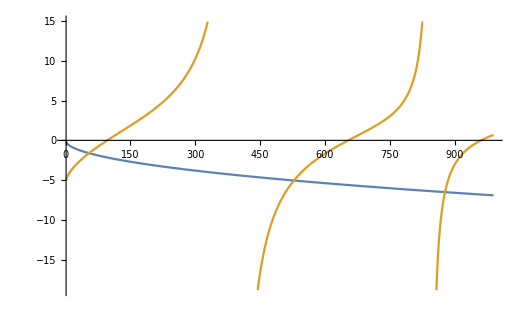

```mathematica
Plot[{lhs[e,1000], rhs[e,1000]},{e,1,990}]
```

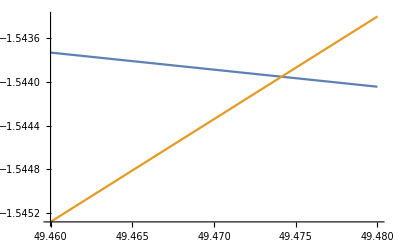

```mathematica
Plot[{lhs[e,100], rhs[e,100]},{e,49.46,49.48}]
```

```mathematica
NSolve[lhs[e,100]-rhs[e,100]==0,e]
```

NSolve[-0.219505 √e-(0.0000363223 (938. √(100-e) √e Cos[0.219505 √(100-e)]+938. (-100+e) Sin[0.219505 √(100-e)]))/(0.155214 √(100-e) Cos[0.219505 √(100-e)]+0.155214 √e Sin[0.219505 √(100-e)])==0,e]

```mathematica
Clear[a]
```

```mathematica
Clear[hbar]
```

```mathematica
Clear[m]
```

```mathematica
Clear[aA]
```

```mathematica
ψI[e,u,0]
```

aA

In this section, we will determine the constants for a normalized wavefunction.   This uses the continuity equation.  We redefine the wave
functions in terms of just the remaining cC constant.  We then integrated to find cC

```mathematica
ψII[e,u,0]
```

cC+(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))

```mathematica
ψI[e,u,0]-ψII[e,u,0]
```

aA-cC-(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))

```mathematica
Solve[ψI[e,u,0]-ψII[e,u,0]==0, aA]
```

{{aA→(-(2 cC e m)/hbar^2+2 ⅈ cC √((e m)/hbar^2) √(-(m (e-u))/hbar^2)+(2 cC m u)/hbar^2)/((e m)/hbar^2-(m (e-u))/hbar^2)}}

```mathematica
ψI[e,u,x]
```

aA ⅇ^(√2 √((e m)/hbar^2) x)

```mathematica
Clear[aA]
```

```mathematica
aA[e_,u_]:=(-(2 cC e m)/hbar^2+2 ⅈ cC √((e m)/hbar^2) √(-(m (e-u))/hbar^2)+(2 cC m u)/hbar^2)/((e m)/hbar^2-(m (e-u))/hbar^2)
```

```mathematica
ψI[e_,u_,x_]:=aA[e,u]*ⅇ^(√2 √((e m)/hbar^2) x)
```

```mathematica
ψI[e,u,x]
```

(ⅇ^(√2 √((e m)/hbar^2) x) (-(2 cC e m)/hbar^2+2 ⅈ cC √((e m)/hbar^2) √(-(m (e-u))/hbar^2)+(2 cC m u)/hbar^2))/((e m)/hbar^2-(m (e-u))/hbar^2)

```mathematica
Solve[ψII[e,u,a]-ψIII[e,u,a]==0,gG]
```

{{gG→-ⅇ^(√2 a √((e m)/hbar^2)) (-cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2))-(ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2)))}}

```mathematica
ψIII[e,u,x]
```

ⅇ^(-√2 √((e m)/hbar^2) x) gG

```mathematica
Clear[gG]
```

```mathematica
gG[e_,u_]:=-ⅇ^(√2 a √((e m)/hbar^2)) (-cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2))-(ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2)))
```

```mathematica
ψIII[e_,u_,x_]:=gG[e,u]*ⅇ^(-√2 √((e m)/hbar^2) x)
```

```mathematica
ψIII[e,u,x]
```

-ⅇ^(√2 a √((e m)/hbar^2)-√2 √((e m)/hbar^2) x) (-cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2))-(ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2)))

```mathematica
ψI[e,u,x]
```

(ⅇ^(√2 √((e m)/hbar^2) x) (-(2 cC e m)/hbar^2+2 ⅈ cC √((e m)/hbar^2) √(-(m (e-u))/hbar^2)+(2 cC m u)/hbar^2))/((e m)/hbar^2-(m (e-u))/hbar^2)

```mathematica
Clear[dD]
```

```mathematica
dD[e_,u_]:=(-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))
```

```mathematica
ψII[e_,u_,x_]:=cC*Exp[I*k[e,u]*x]+ dD[e,u]*Exp[-I*k[e,u]*x]
```

```mathematica
ψII[e,u,x]
```

cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x)+(ⅇ^(-ⅈ √2 √((m (-e+u))/hbar^2) x) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2))

```mathematica
ψIII[e,u,x]
```

-ⅇ^(√2 a √((e m)/hbar^2)-√2 √((e m)/hbar^2) x) (-cC ⅇ^(ⅈ √2 a √((m (-e+u))/hbar^2))-(ⅇ^(-ⅈ √2 a √((m (-e+u))/hbar^2)) (-cC √((e m)/hbar^2)+ⅈ cC √(-(m (e-u))/hbar^2)))/(√((e m)/hbar^2)+ⅈ √(-(m (e-u))/hbar^2)))

```mathematica
m=938.0
```

938.

```mathematica
hbar=197.32
```

197.32

```mathematica
Element[a,Reals]
```

a∈ℝ

```mathematica
Element[u,Reals]
```

u∈ℝ

```mathematica
Element[e,Reals]
```

e∈ℝ

```mathematica
a=1.0
```

1.

```mathematica
ψI[49.47,100,x]
```

(1.0106+0.999944 ⅈ) cC ⅇ^(1.54389 x)

```mathematica
ψII[49.47,100,x]
```

(0.0106+0.999944 ⅈ) cC ⅇ^((0.-1.56034 ⅈ) x)+cC ⅇ^((0.+1.56034 ⅈ) x)

```mathematica
ψIII[49.47,100,x]
```

(4.73172+4.68183 ⅈ) cC ⅇ^(-1.54389 x)

```mathematica
Integrate[Conjugate[ψI[49.47,100,x]]*ψI[49.47,100,x],{x,-Infinity,0}]+Integrate[Conjugate[ψII[49.47,100,x]]*ψII[49.47,100,x],{x,0,a}]+Integrate[Conjugate[ψIII[49.47,100,x]]*ψIII[49.47,100,x],{x,a,Infinity}]
```

4.59067 cC Conjugate[cC]

```mathematica
cC=Sqrt[1.0/4.590670944957337]
```

0.466726

```mathematica
fullψ[e_,u_,x_]:=ψI[e,u,x]*HeavisideTheta[-x]+ψII[e,u,x]*HeavisideTheta[x]*HeavisideTheta[a-x]+ψIII[e,u,x]*HeavisideTheta[x-a]
```

```mathematica
fullψ[49.47,100,x]
```

(2.20842+2.18513 ⅈ) ⅇ^(-1.54389 x) HeavisideTheta[-1.+x]+(0.471673+0.4667 ⅈ) ⅇ^(1.54389 x) HeavisideTheta[-x]+((0.00494729+0.4667 ⅈ) ⅇ^((0.-1.56034 ⅈ) x)+0.466726 ⅇ^((0.+1.56034 ⅈ) x)) HeavisideTheta[1.-x] HeavisideTheta[x]

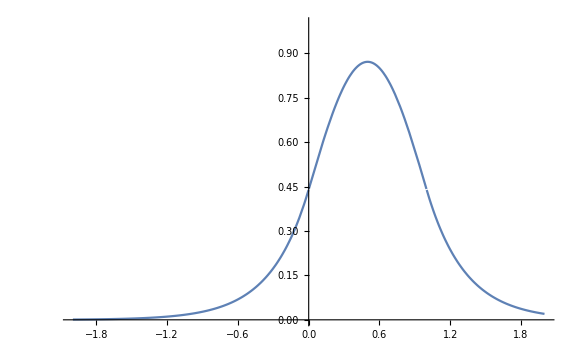

```mathematica
Plot[Conjugate[fullψ[49.47,100,x]]*fullψ[49.47,100,x],{x, -2*a, +2*a},PlotRange->{0,1}]
```

```mathematica
Integrate[Conjugate[ψI[49.47,100,x]]*(-I*hbar)*D[ψI[49.47,100,x],x],{x,-Infinity,0}]+Integrate[Conjugate[ψII[49.47,100,x]]*-I*hbar*D[ψII[49.47,100,x],x],{x,0,a}]+Integrate[Conjugate[ψIII[49.47,100,x]]*-I*hbar*D[ψIII[49.47,100,x],x],{x,a,Infinity}]
```

-1.08528×10^-14+4.26326×10^-14 ⅈ

```mathematica
Integrate[Conjugate[ψI[49.47,100,x]]*x*ψI[49.47,100,x],{x,-Infinity,0}]+Integrate[Conjugate[ψII[49.47,100,x]]*x*ψII[49.47,100,x],{x,0,a}]+Integrate[Conjugate[ψIII[49.47,100,x]]*x*ψIII[49.47,100,x],{x,a,Infinity}]
```

0.499953+6.93889×10^-18 ⅈ